```mathematica
(* STOP UNLESS WANT TO ANALYZE ITERATIVE PROCEDURE *)

(* STOP UNLESS WANT TO ANALYZE ITERATIVE PROCEDURE *)
```

```mathematica
(* DampingFactor->1000,MaxIterations->1000, *)
(* DampingFactor->(10^(Range[0,100])) *)
```

```mathematica
(* myvars*)
```

```mathematica
mysol
```

{d→4.13206×10^-14,ux→7.10134×10^-12,rhoc→15.2166,iec→41546.6,rhoout→15.2339,ieout→2.14638×10^-18,Bx→4.06552×10^-9,uy→-240.262}

```mathematica
(* check -uy for relativistic outflow *)
vel4togorel=2.0;
If[(Abs[mysolnonrel[[8,2]]]>vel4togorel||Abs[mysolnonrelconverted[[8,2]]]>vel4togorel),mysol=mysolmixedrel;Print["Using mixedrel"];,mysol=mysolnonrelconverted;Print["Using convertedrel"];];
(* form guess for rel calculation *)
myvars=formnonrelguess[mysol];
(* start rel calculation process *)
solvespfullsetup1;
solvespfullsetup2;
```

Using mixedrel

Slund=1.×10^25

sigma=13848.9

```mathematica
SetPrecision[mysol,10]
```

{d→1.47807464×10^-14,ux→6.765436072×10^-12,rhoc→15.1281115,iec→41546.59114,rhoout→15.1281115,ieout→3.803405766×10^-18,Bx→3.991377412×10^-9,uy→-30.256223}

```mathematica
(*factor=1.2;
myothervars=Table[{myvars[[ii,1]],myvars[[ii,2]]/factor,myvars[[ii,2]]*factor},{ii,1,8}]
supersol=FindRoot[nummyeqns0,myothervars,Method->"Secant",WorkingPrecision->400,MaxIterations->10000]
*)
```

```mathematica
eqnscompact//.constssprel//.fsolsspotherunits
eqnsfull//.constssprel//.fsolsspotherunits
```

{2.65028×10^-12,-2.52376×10^-7,7.3067×10^-9,-0.000655288,-4.49278×10^-14,0.,0.000712307,-7.30688×10^-9}

{2.65071×10^-12,1.08583×10^-7,-1.06103×10^-8,-0.000655288,-4.49278×10^-14,0.,-0.000293751,1.06102×10^-8}

```mathematica
fakesol={d->5.08802164279888*^-12,ux->2.3187711410977482*^-12,rhoc->0.24999999965379335,iec->2.49229312720997,rhoout->0.24999999965379335,ieout->4.2400712877343714*^-23,Bx->8.49783227176429*^-12,uy->-1.8229255353822011};
fakesol1={ux->2.3187711410977482*^-12,rhoc->0.24999999965379335,iec->2.49229312720997,rhoout->0.24999999965379335,ieout->4.2400712877343714*^-23,Bx->8.49783227176429*^-12,uy->-1.8229255353822011};
fakesol2={d->5.08802164279888*^-12,rhoc->0.24999999965379335,iec->2.49229312720997,rhoout->0.24999999965379335,ieout->4.2400712877343714*^-23,Bx->8.49783227176429*^-12,uy->-1.8229255353822011};
fakesol3={d->5.08802164279888*^-12,ux->2.3187711410977482*^-12,iec->2.49229312720997,rhoout->0.24999999965379335,ieout->4.2400712877343714*^-23,Bx->8.49783227176429*^-12,uy->-1.8229255353822011};
fakesol4={d->5.08802164279888*^-12,ux->2.3187711410977482*^-12,rhoc->0.24999999965379335,rhoout->0.24999999965379335,ieout->4.2400712877343714*^-23,Bx->8.49783227176429*^-12,uy->-1.8229255353822011};
fakesol5={d->5.08802164279888*^-12,ux->2.3187711410977482*^-12,rhoc->0.24999999965379335,iec->2.49229312720997,ieout->4.2400712877343714*^-23,Bx->8.49783227176429*^-12,uy->-1.8229255353822011};
fakesol6={d->5.08802164279888*^-12,ux->2.3187711410977482*^-12,rhoc->0.24999999965379335,iec->2.49229312720997,rhoout->0.24999999965379335,Bx->8.49783227176429*^-12,uy->-1.8229255353822011};
fakesol7={d->5.08802164279888*^-12,ux->2.3187711410977482*^-12,rhoc->0.24999999965379335,iec->2.49229312720997,rhoout->0.24999999965379335,ieout->4.2400712877343714*^-23,uy->-1.8229255353822011};
fakesol8={d->5.08802164279888*^-12,ux->2.3187711410977482*^-12,rhoc->0.24999999965379335,iec->2.49229312720997,rhoout->0.24999999965379335,ieout->4.2400712877343714*^-23,Bx->8.49783227176429*^-12};
```

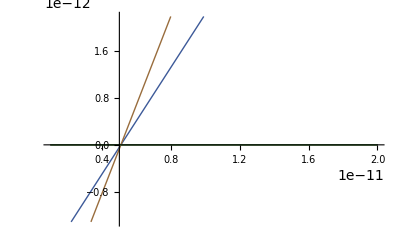

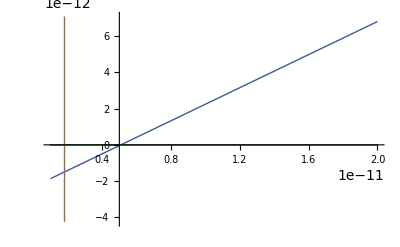

NSolve::precw: The precision of the argument function ({-4.569396683208058` (1.5027593750384267`*^-28 - 2.392354394765377`*^-17 d) + 1.2770197113897879`*^-39 d}) is less than WorkingPrecision (400).

{{d→6.281508200986272834562341885383858925531932376597844816008019000993073290060867526302396275721352853405073843003071422581369740255976795480127360224630934448100466729138786737676355211730473945252959423517322379324520347376876133697426239462951837806779796477395304540360924551761719549536815307409208887981983966824816640352279205954082146019215889927875738187917161542717739545548566145710340291938×10^-12}}

NSolve::precw: The precision of the argument function ({-1.4277225353261818`*^-27 + 1.5982499947311035`*^-16 d}) is less than WorkingPrecision (400).

{{d→8.933036383750390032607249821154758383859648967607347138954517326965840947242441935528039957166898219157422121427762426430945844405517908334039081009922383242406062739139835874349441256733036255364195241257254549152528619405085281859735960897049492160115357653157405119466261262950358394325967679947421833175477045436561368035083224899456901393423382711489051550781494731837902401850035177086748191138×10^-12}}

{}

{}

NSolve::precw: The precision of the argument function ({1.`200. (2.318771141097748`*^-12 - 0.45573138321444134` d)}) is less than WorkingPrecision (400).

{{d→5.088021642798880900952050613883857032237954956307322100470560755775324131646162502318802764542141851900332556079341717110095646094591531723706939985440241219557449166087793638293590729580556561415492949253848724635771419776580088201381555563591720089166471935299164815566317155058529196871631796881323146660126581443806430337419153893804952445231171953970048700559591366765065560463119128870356897791×10^-12}}

{{}}

NSolve::precw: The precision of the argument function ({-8741.25174038592` (-3.85270492435582`*^-12 + 2.1261819240499658` d)}) is less than WorkingPrecision (400).

{{d→1.812029761318430178716069583598067735103355609561634591495480749331405657191150219906169534081600115682198918194495560281319292831407567637645724926886473809480598243417524233052904191045317083583592355387466561162440519346707239669035869181755789504499417561604144613640319539720538690246001677060767738518501234598011478782824368569443624805923146299431510774657260186119903664785287083365380750203×10^-12}}

{}

```mathematica
one=eqnscompact//.constssprel//.fakesol1;
two=eqnsfull//.constssprel//.fakesol1;
Plot[{one},{d,10^(-12),2*10^(-11)}]
Plot[{two},{d,10^(-12),2*10^(-11)}]
NSolve[0==two[[1]],d,WorkingPrecision->400]
NSolve[0==two[[2]],d,WorkingPrecision->400]
NSolve[0==two[[3]],d,WorkingPrecision->400]
NSolve[0==two[[4]],d,WorkingPrecision->400]
NSolve[0==two[[5]],d,WorkingPrecision->400]
NSolve[0==two[[6]],d,WorkingPrecision->400]
NSolve[0==two[[7]],d,WorkingPrecision->400]
NSolve[0==two[[8]],d,WorkingPrecision->400]
```

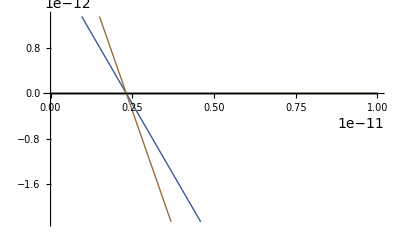

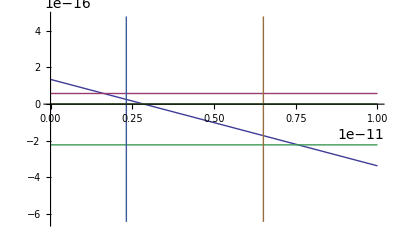

NSolve::precw: The precision of the argument function ({-0.00001031733728423406736138009658967277091679702210025773398697856759713674193827033037548023126243214451927188973112083761026137415990558818390220864736021359625365054210477521519644710311898736648725573808856634158656964`200. (-4.569396683208058362879455671645700931549072265625`200. ux/1 + ux^2 - « 115 » (8.49783227176429`*^-12 - 8.980694273726536`*^11/√1 + Power[« 2 »]))}) is less than WorkingPrecision (400).

{{ux→-3.691721149311457696214143755042663004172733435926251267040201522728920676416308609118827132176467123790669715839101953319464875898914070554443384563422347790347324292727987509078935933363396035795841470014801936641993491659567756851556436469898481002867375678520744985872392389828539263786000864215483329609870118697962684871405996932339157716158487389491418588881392357756134086378342683586836×10^34},{ux→2.8626804211083315951728693676104531520947220563619185399218429180895217100644639364827200521660744275754350643023253733457080544885154333422919466064218165690435010034466374591448637507473238347022387692076161725844147074927192263954393565389187262078253143672426053490350256419788727977146550648977396178350709799219997807240327956453687033634282803661964192070928816683366340238455531898344144×10^-12}}

NSolve::precw: The precision of the argument function ({-0.00001031733728423406736138009658967277091679702210025773398697856759713674193827033037548023126243214451927188973112083761026137415990558818390220864736021359625365054210477521519644710311898736648725573808856634158656964`200. (-7.450434088018566`*^-12 - 1.4565379939015803655257659862636634030387838577633309858477546165633764729818722116760909557342529296875`200.*^-23 (8.49783227176429`*^-12 - « 1 »))}) is less than WorkingPrecision (400).

{{ux→-1.443080133453168918358749780940056563623232779105190787490823196203576378704542863834063691617376448749922652258700659714950801431718296050453861890647276218725584627814134035867118786183262680011813513004603442220910561331406522949831151603507613253809032713170157125889470975034289484214837417731586715696701745153197449848931045296851609009657516625745527937372346221021837071483068704520716729},{ux→1.443080133453168918358749780940056563623232779105190787490823196203576378704542863834063691617376448749922652258700659714950801431718296050453861890647276218725584627814134035867118786183262680011813513004603442220910561331406522949831151603507613253809032713170157125889470975034289484214837417731586715696701745153197449848931045296851609009657516625745527937372346221021837071483068704520716729}}

NSolve::precw: The precision of the argument function ({0.8307643745861922`  - « 233 »/(1 + ux^2)^2 - ux^2 (1.00000000460185775528798206524652384998471295792417852984120448430379231770833333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333`199.9999999980014 + « 232 »/(1 + ux^2)^2)}) is less than WorkingPrecision (400).

{{ux→-0.4557313821658359131713518062357196581852219402148692475487685687847986538617254803263832119700153305704895984523503063908267794278547332636981026794275531458505206520755317163772406158879409435671240078895620928180377431317283477619483804610567781593623019365251892097087997388207178444607694352749607381645895934073716148642573205304247672099938822513979587378191017124270229468+0.8901173559195533427109274014492469092621991946214411044439012142702868845235072104801402273175659298024927550432563217595554313844602272642276463955163460279665366876840875414326437580931555044176518827033523174793369679319133989595010354034118480497898784696779409766628978194495050554727957843667328591938500067487465761084317154216439795479891338301498483674635479622776314707 ⅈ},{ux→-0.4557313821658359131713518062357196581852219402148692475487685687847986538617254803263832119700153305704895984523503063908267794278547332636981026794275531458505206520755317163772406158879409435671240078895620928180377431317283477619483804610567781593623019365251892097087997388207178444607694352749607381645895934073716148642573205304247672099938822513979587378191017124270229468-0.8901173559195533427109274014492469092621991946214411044439012142702868845235072104801402273175659298024927550432563217595554313844602272642276463955163460279665366876840875414326437580931555044176518827033523174793369679319133989595010354034118480497898784696779409766628978194495050554727957843667328591938500067487465761084317154216439795479891338301498483674635479622776314707 ⅈ},{ux→0.4557313821658359131713518062357196581852219402148692475487685687847986538617254803263832119700153305704895984523503063908267794278547332636981026794275531458505206520755317163772406158879409435671240078895620928180377431317283477619483804610567781593623019365251892097087997388207178444607694352749607381645895934073716148642573205304247672099938822513979587378191017124270229468+0.8901173559195533427109274014492469092621991946214411044439012142702868845235072104801402273175659298024927550432563217595554313844602272642276463955163460279665366876840875414326437580931555044176518827033523174793369679319133989595010354034118480497898784696779409766628978194495050554727957843667328591938500067487465761084317154216439795479891338301498483674635479622776314707 ⅈ},{ux→0.4557313821658359131713518062357196581852219402148692475487685687847986538617254803263832119700153305704895984523503063908267794278547332636981026794275531458505206520755317163772406158879409435671240078895620928180377431317283477619483804610567781593623019365251892097087997388207178444607694352749607381645895934073716148642573205304247672099938822513979587378191017124270229468-0.8901173559195533427109274014492469092621991946214411044439012142702868845235072104801402273175659298024927550432563217595554313844602272642276463955163460279665366876840875414326437580931555044176518827033523174793369679319133989595010354034118480497898784696779409766628978194495050554727957843667328591938500067487465761084317154216439795479891338301498483674635479622776314707 ⅈ},{ux→5.362921635428058841964958633072680154706617908136345912672610308693721260458669564392684893694700489398832735436447337574917554764146167667400678089009044554346853977592791941370048382290310724731327421476371283139433933247826479297636903512982183492183750908671423688033349988200255289484285505162234510382942731738788822785445389978630814178494244769873841621110620490456368111×10^-9},{ux→-5.362921635428058841964958633072680154706617908136345912672610308693721260458669564392684893694700489398832735436447337574917554764146167667400678089009044554346853977592791941370048382290310724731327421476371283139433933247826479297636903512982183492183750908671423688033349988200255289484285505162234510382942731738788822785445389978630814178494244769873841621110620490456368111×10^-9}}

{}

NSolve::precw: The precision of the argument function ({-1.`199.69897000433602 (2.318771141097748`*^-12 - 0.99999999999999988897769753748434595763683319091796875`199.5228787452803 ux)}) is less than WorkingPrecision (400).

{{ux→2.318771141097748372608515585074669627318060021350395563875223027286390448018868834413029200840344834412622960356575706393689624083651594692821870651519101727252911939045831847783522401436037840760310444847163666150277882475755278390585885115724736996533718077500828631194355714583158384898771544954337099239458322170436708594896522213968204702398728187332135348635167530584550583177436437263961332715×10^-12}}

{{}}

NSolve::precw: The precision of the argument function ({-1.`199.69897000433602 (1.0818059646093989`*^-11 - 1.`199.69897000433602 ux √1 + ux^2 (4.60185786631028452776217789234787976700620977984120448430379231770833333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333332`199.69897000433602*^-9 + « 232 »/(1 + « 1 »)^2 + « 60 » (ux^2 + ux^4)/1 + Power[« 2 »] + Power[« 2 »]))}) is less than WorkingPrecision (400).

{{ux→0.10368392623589788919411189816384849665560822438500179470713095172253867307958808364737482281027966506550338445102609147710918311135002260330479577506517062884641316173123569138946581554517585765983598018264848135842940701470954248025531411005346803282105250106182401666471608852741840995786833404748347697+1.43473715411501907578968098271106048144746106479206337302137127350503636484078125004881246791527692694900211040999377670487905914979154150556012648925871692221211794266996239612653890957430525915351160137972477148206895734698123900614689878673433869981470115037309195245784985687631799037379166756865795403 ⅈ},{ux→0.10368392623589788919411189816384849665560822438500179470713095172253867307958808364737482281027966506550338445102609147710918311135002260330479577506517062884641316173123569138946581554517585765983598018264848135842940701470954248025531411005346803282105250106182401666471608852741840995786833404748347697-1.43473715411501907578968098271106048144746106479206337302137127350503636484078125004881246791527692694900211040999377670487905914979154150556012648925871692221211794266996239612653890957430525915351160137972477148206895734698123900614689878673433869981470115037309195245784985687631799037379166756865795403 ⅈ},{ux→-0.10368392623529547863133523014759817885647059685760378683463906505068011589938114508401674009694629541185827290411756853212068786595261898454216031960541635932875898494153111236202333885412785183751426116503678738087888855761292664885056091636981221186372811238611798577425367324906527742211801048518306147+1.43473715411375242412488620488261478457697044918731764778136679794572585018435650633131523540205733631449395263773293144179028482005448285119006503515532459140015900228513179986415025768521493761757059130758253467050475130523143576863873862622405536168779444943131696271780829158735333566530210324727907801 ⅈ},{ux→-0.10368392623529547863133523014759817885647059685760378683463906505068011589938114508401674009694629541185827290411756853212068786595261898454216031960541635932875898494153111236202333885412785183751426116503678738087888855761292664885056091636981221186372811238611798577425367324906527742211801048518306147-1.43473715411375242412488620488261478457697044918731764778136679794572585018435650633131523540205733631449395263773293144179028482005448285119006503515532459140015900228513179986415025768521493761757059130758253467050475130523143576863873862622405536168779444943131696271780829158735333566530210324727907801 ⅈ},{ux→-0.80119171858270906122145137462438673865060983401677948300227975185920909987222144085932701424316913661580836644842603481142569279718865412023597500402004206683352573518572380382058148173838701005231373549313350771378846635615057342176189363914408681479093868732730293411508546052470314921802147631378115689+0.697992856961416951057562210454712377229263914591925050421452944871479101070820045588577240098321498119744675757612767664623396514476583818666365396127803063886252544646634357472296094881357474199772930957024224150699771335909827540654145208631913934615684575839901853122080388964250164407328761874131670782 ⅈ},{ux→-0.80119171858270906122145137462438673865060983401677948300227975185920909987222144085932701424316913661580836644842603481142569279718865412023597500402004206683352573518572380382058148173838701005231373549313350771378846635615057342176189363914408681479093868732730293411508546052470314921802147631378115689-0.697992856961416951057562210454712377229263914591925050421452944871479101070820045588577240098321498119744675757612767664623396514476583818666365396127803063886252544646634357472296094881357474199772930957024224150699771335909827540654145208631913934615684575839901853122080388964250164407328761874131670782 ⅈ},{ux→0.801191718578760050287353602243107832721827839183077186466680164153123807323596448739191840737547129201132961048189023891727150046388541765840865108840974587569053076624154895964113636651594609552900743565461459981853714454960559586996705318157724390248667077308484126363012237150418418950865374753076236929+0.697992856957660004673675629135771137436074891382437602064511726958558607453555536991260059699186552269553353924200034444064978613634900161052673660634915521417515561447660439415351461966836202017090741641372176136071190426052105653675298223567314054124209634960277851410527932148805886160614544125497613671 ⅈ},{ux→0.801191718578760050287353602243107832721827839183077186466680164153123807323596448739191840737547129201132961048189023891727150046388541765840865108840974587569053076624154895964113636651594609552900743565461459981853714454960559586996705318157724390248667077308484126363012237150418418950865374753076236929-0.697992856957660004673675629135771137436074891382437602064511726958558607453555536991260059699186552269553353924200034444064978613634900161052673660634915521417515561447660439415351461966836202017090741641372176136071190426052105653675298223567314054124209634960277851410527932148805886160614544125497613671 ⅈ},{ux→6.51090727230584943038325391906287340936601356380214519754979231052878525508854476449276101271343119210417098188713972764059967486070240213719192272713726997871992609707162131851597703501450470444158684585801174538559650873405916431473704620163028161204559909538144321937592485183770607457815823234733801632×10^-12}}

NSolve::precw: The precision of the argument function ({-0.8307643745861922` + « 233 »/(1 + ux^2)^2}) is less than WorkingPrecision (400).

{{ux→1.4142135623730950426817080568634280552989376432126730783254889877759376363157828482190775106412907517184575291629338356197247093607148194545792550370579761329450973306958523158920200562092137885637903669230600836836599263131772528203360720829243819265382827228568731961109264048376885455433281253073705115923541577477662195090135609951510163391963302605115127544259414322233882125 ⅈ},{ux→-1.4142135623730950426817080568634280552989376432126730783254889877759376363157828482190775106412907517184575291629338356197247093607148194545792550370579761329450973306958523158920200562092137885637903669230600836836599263131772528203360720829243819265382827228568731961109264048376885455433281253073705115923541577477662195090135609951510163391963302605115127544259414322233882125 ⅈ},{ux→4.1605191169425577064458768105883818149286335172592992206057643633970145983653075022965101957483350030920255010536722787607897173683053880075767937385985216736881019654290523916931973368685998768622524148856060925768977014735621065155969447055404262657805129346491837381367630860767261032045833771871475720210373943168400846407929520115584345497972232990533007744346947231552658183×10^-9 ⅈ},{ux→-4.1605191169425577064458768105883818149286335172592992206057643633970145983653075022965101957483350030920255010536722787607897173683053880075767937385985216736881019654290523916931973368685998768622524148856060925768977014735621065155969447055404262657805129346491837381367630860767261032045833771871475720210373943168400846407929520115584345497972232990533007744346947231552658183×10^-9 ⅈ}}

```mathematica
one=eqnscompact//.constssprel//.fakesol2;
two=eqnsfull//.constssprel//.fakesol2;
Plot[{one},{ux,0,10^(-11)}]
Plot[{two},{ux,0,10^(-11)}]
NSolve[0==two[[1]],ux,WorkingPrecision->400]
NSolve[0==two[[2]],ux,WorkingPrecision->400]
NSolve[0==two[[3]],ux,WorkingPrecision->400]
NSolve[0==two[[4]],ux,WorkingPrecision->400]
NSolve[0==two[[5]],ux,WorkingPrecision->400]
NSolve[0==two[[6]],ux,WorkingPrecision->400]
NSolve[0==two[[7]],ux,WorkingPrecision->400]
NSolve[0==two[[8]],ux,WorkingPrecision->400]
```

```mathematica
one=eqnscompact//.constssprel//.fakesol3;
two=eqnsfull//.constssprel//.fakesol3;
Plot[{one},{rhoc,0,1}]
Plot[{two},{rhoc,0,1}]
NSolve[0==two[[1]],rhoc,WorkingPrecision->400]
NSolve[0==two[[2]],rhoc,WorkingPrecision->400]
NSolve[0==two[[3]],rhoc,WorkingPrecision->400]
NSolve[0==two[[4]],rhoc,WorkingPrecision->400]
NSolve[0==two[[5]],rhoc,WorkingPrecision->400]
NSolve[0==two[[6]],rhoc,WorkingPrecision->400]
NSolve[0==two[[7]],rhoc,WorkingPrecision->400]
NSolve[0==two[[8]],rhoc,WorkingPrecision->400]
```

```mathematica
one=eqnscompact//.constssprel//.fakesol4;
two=eqnsfull//.constssprel//.fakesol4;
Plot[{one},{iec,0,3}]
Plot[{two},{iec,0,3}]
NSolve[0==two[[1]],iec,WorkingPrecision->400]
NSolve[0==two[[2]],iec,WorkingPrecision->400]
NSolve[0==two[[3]],iec,WorkingPrecision->400]
NSolve[0==two[[4]],iec,WorkingPrecision->400]
NSolve[0==two[[5]],iec,WorkingPrecision->400]
NSolve[0==two[[6]],iec,WorkingPrecision->400]
NSolve[0==two[[7]],iec,WorkingPrecision->400]
NSolve[0==two[[8]],iec,WorkingPrecision->400]
```

```mathematica
one=eqnscompact//.constssprel//.fakesol5;
two=eqnsfull//.constssprel//.fakesol5;
Plot[{one},{rhoout,0,3}]
Plot[{two},{rhoout,0,3}]
NSolve[0==two[[1]],rhoout,WorkingPrecision->400]
NSolve[0==two[[2]],rhoout,WorkingPrecision->400]
NSolve[0==two[[3]],rhoout,WorkingPrecision->400]
NSolve[0==two[[4]],rhoout,WorkingPrecision->400]
NSolve[0==two[[5]],rhoout,WorkingPrecision->400]
NSolve[0==two[[6]],rhoout,WorkingPrecision->400]
NSolve[0==two[[7]],rhoout,WorkingPrecision->400]
NSolve[0==two[[8]],rhoout,WorkingPrecision->400]
```

```mathematica
one=eqnscompact//.constssprel//.fakesol6;
two=eqnsfull//.constssprel//.fakesol6;
Plot[{one},{ieout,0,3}]
Plot[{two},{ieout,0,3}]
NSolve[0==two[[1]],ieout,WorkingPrecision->400]
NSolve[0==two[[2]],ieout,WorkingPrecision->400]
NSolve[0==two[[3]],ieout,WorkingPrecision->400]
NSolve[0==two[[4]],ieout,WorkingPrecision->400]
NSolve[0==two[[5]],ieout,WorkingPrecision->400]
NSolve[0==two[[6]],ieout,WorkingPrecision->400]
NSolve[0==two[[7]],ieout,WorkingPrecision->400]
NSolve[0==two[[8]],ieout,WorkingPrecision->400]
```

```mathematica
one=eqnscompact//.constssprel//.fakesol7;
two=eqnsfull//.constssprel//.fakesol7;
Plot[{one},{Bx,0,3}]
Plot[{two},{Bx,0,3}]
NSolve[0==two[[1]],Bx,WorkingPrecision->400]
NSolve[0==two[[2]],Bx,WorkingPrecision->400]
NSolve[0==two[[3]],Bx,WorkingPrecision->400]
NSolve[0==two[[4]],Bx,WorkingPrecision->400]
NSolve[0==two[[5]],Bx,WorkingPrecision->400]
NSolve[0==two[[6]],Bx,WorkingPrecision->400]
NSolve[0==two[[7]],Bx,WorkingPrecision->400]
NSolve[0==two[[8]],Bx,WorkingPrecision->400]
```

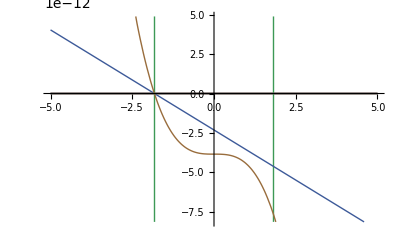

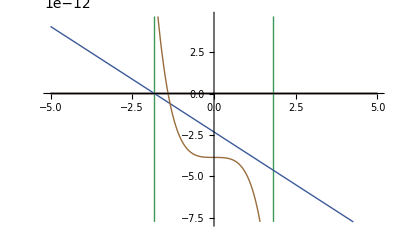

{}

NSolve::precw: The precision of the argument function ({-0.00001031733728423406736138009658967277091679702210025773398697856759713674193827033037548023126243214451927188973112083761026137415990558818390220864736021359625365054210477521519644710311898736648725573808856634158656964`200. (1.3080722421297059`*^-11 + 8.49783227176429`*^-12 uy/√1 + uy^2)}) is less than WorkingPrecision (400).

{{uy→-1.31537877479278073855574734834561443096463888070124336302765910661156857929234808455337401290677488841239211502130393304927947988970146620031959714006718977524868249865261687206664384285604125504824675071850095551634974770665039825524872310575104241144513352672679918277290022989477972525243841563360085155570018629821570928793343293375140185883303058370363582481223749673620887924711785423543717 ⅈ}}

{{}}

NSolve::precw: The precision of the argument function ({0.8307643757366567`  - 2.873270076744477`*^-24/1 + uy^2 - uy^2 (0.24999999965379335`  + 5.746540153488954`*^-24/1 + uy^2)}) is less than WorkingPrecision (400).

{{uy→-1.822925535382201312603063074075470010139251034235239241376188322933858637212873443054562830792551343537180761381745493167052408554942470362699750702772806991163459985527370069939904408940973826139761002171573399162935672934483806245377774211394656024864905104307452266414827632191268506959057340730882064387352345269448332309560306192494657945901264829911041802993324474988390927344831956987246},{uy→1.822925535382201312603063074075470010139251034235239241376188322933858637212873443054562830792551343537180761381745493167052408554942470362699750702772806991163459985527370069939904408940973826139761002171573399162935672934483806245377774211394656024864905104307452266414827632191268506959057340730882064387352345269448332309560306192494657945901264829911041802993324474988390927344831956987246},{uy→1.00000000000000000000000132927682581434296483846757859763535588428016739328938615481398640487381720852970276802778730915618665739138766365191909386398164973946701644402075083055165863253069245298706773151960853543703254475066063493903110575658657792402042166202386481182311122459428473684990740762146288768374353537888345686605940310409095701120659376904238049871492579578854624340338918494489886 ⅈ},{uy→-1.00000000000000000000000132927682581434296483846757859763535588428016739328938615481398640487381720852970276802778730915618665739138766365191909386398164973946701644402075083055165863253069245298706773151960853543703254475066063493903110575658657792402042166202386481182311122459428473684990740762146288768374353537888345686605940310409095701120659376904238049871492579578854624340338918494489886 ⅈ}}

NSolve::precw: The precision of the argument function ({-1.`199.69897000433602 (-2.318771141097748`*^-12 - 1.2720054089382131`*^-12 uy)}) is less than WorkingPrecision (400).

{{uy→-1.822925535382201355658421148793960860596296224882055929775940967657694092631885888276354334687164866133071441835766019970066196838707243325985192311756386472713069240529446639025406485939936943688143930371603479201845575039658566072302332555341995344593336344047869378407617836413342465733323033208835588245875080076846345481561599370642331222373182837492265523540065626151512485457425128114208126499}}

{{}}

NSolve::precw: The precision of the argument function ({-1.`199.69897000433602 (-3.852704924355819`*^-12 - 5.08802164279888`*^-12 uy √1 + uy^2 (5.653428383645828`*^-23 + 5.746540153488954`*^-24/1 + Power[« 2 »] + 0.24999999965379335` (uy^2 + uy^4)/1 + Power[« 2 »] + Power[« 2 »]))}) is less than WorkingPrecision (400).

{{uy→-0.19777166205469011861913828373057061637780333892201671133255262094902345089128450392243030518142183935618931715547139025575408916262501210067573507932462691172562641983279860498804174130518300956728638641952524725840412183306233936428711500868602778814527945168629138521693844669+1.52640895253154916671361204532004941372773569857900389758268509799144985816261178580128101556609042926796394291542876219272766153490158553486303408758987647239865820577891656893928333138384885462594387447824312390160594438375768574627137455107467216020434581771371643703236950622 ⅈ},{uy→-0.19777166205469011861913828373057061637780333892201671133255262094902345089128450392243030518142183935618931715547139025575408916262501210067573507932462691172562641983279860498804174130518300956728638641952524725840412183306233936428711500868602778814527945168629138521693844669-1.52640895253154916671361204532004941372773569857900389758268509799144985816261178580128101556609042926796394291542876219272766153490158553486303408758987647239865820577891656893928333138384885462594387447824312390160594438375768574627137455107467216020434581771371643703236950622 ⅈ},{uy→1.0350083907450846627093879784921113999144449396745415940882385632848886386440533404071003126792372596223184205536540113449494546461208366674187854107154834651996322138795803515245655761499573958268326163511092896236734888163763303379558132232914575482937383764145658287886525419+1.03342650183667740671324695536844139678092835176756778748605882057805005908720165175753310681745511736663028417272022277752040100661036139772044437629444583520535391393258043941726749494720950825272875097284031496417461923143595432327535869140418507079948846932078973093958413569 ⅈ},{uy→1.0350083907450846627093879784921113999144449396745415940882385632848886386440533404071003126792372596223184205536540113449494546461208366674187854107154834651996322138795803515245655761499573958268326163511092896236734888163763303379558132232914575482937383764145658287886525419-1.03342650183667740671324695536844139678092835176756778748605882057805005908720165175753310681745511736663028417272022277752040100661036139772044437629444583520535391393258043941726749494720950825272875097284031496417461923143595432327535869140418507079948846932078973093958413569 ⅈ},{uy→-1.40516210519665263828435526816082564033130202598865879615249773931546782266444553319547618992347829821861111306978445392253111597210032074873605817260850958588099633885867656085610017009879761309156931056107597886699344454685063544848130394750174808934902532808401521300799626192}}

{{}}

NSolve::precw: The precision of the argument function ({-0.00001031733728423406736138009658967277091679702210025773398697856759713674193827033037548023126243214451927188973112083761026137415990558818390220864736021359625365054210477521519644710311898736648725573808856634158656964`200. (-1.0595385161250615`*^-11 - 1.4565379939015803655257659862636634030387838577633309858477546165633764729818722116760909557342529296875`200.*^-23 (8.49783227176429`*^-12 - « 18 »/d))}) is less than WorkingPrecision (400).

{{d→6.2815082009862726439822033470609771167962060019108594933513554503024316771635664646367777540895399995519160780943810782895061553976011947925416300072855761072483268465527491832503652575821380179817057718436281333577635098299639750683745834654328332118904503931539476190506320893302867874083320591129375298897302842654542754343516981537555801247889862444518204659594911284039198994678717370219210091×10^-12}}

NSolve::precw: The precision of the argument function ({-0.00001031733728423406736138009658967277091679702210025773398697856759713674193827033037548023126243214451927188973112083761026137415990558818390220864736021359625365054210477521519644710311898736648725573808856634158656964`200. (-7.450434088018566`*^-12 - 1.4565379939015803655257659862636634030387838577633309858477546165633764729818722116760909557342529296875`200.*^-23 (8.49783227176429`*^-12 - « 18 »/d))}) is less than WorkingPrecision (400).

{{d→8.9330363837503888938358118221517575317849552071306393315813259371739943542255770525313376635547129112400656594687641658592171938928461152037760842031063756240526688023076871863023565750914822695866872299699720597479110207024373809934469344886848130444724970917818172765148351748941215118880832137570370584453215079255302644390232166960252620190169217016488493247959763726797447382192460294183483747×10^-12}}

{{}}

{}

NSolve::precw: The precision of the argument function ({-1.`199.69897000433602 (-2.318771141097748`*^-12 + 0.45573138321444134` d)}) is less than WorkingPrecision (400).

{{d→5.088021642798880900952050613883857032237954956307322100470560755775324131646162502318802764542141851900332556079341717110095646094591531723706939985440241219557449166087793638293590729580556561415492949253848724635771419776580088201381555563591720089166471935299164815566317155058529196871631796881323146660126581443806430337419153893804952445231171953970048700559591366765065560463119128870356897791×10^-12}}

{{}}

NSolve::precw: The precision of the argument function ({-1.`199.69897000433602 (-3.852704924355819`*^-12 + 2.1261819240499653` d)}) is less than WorkingPrecision (400).

{{d→1.812029761318430389938037791033777537027760262347927157601133509409338913145889707877025713882473722683317037085392731119674567620274887563879352643746208757208133511315705758387117060014489007209885435687713715714713602729891016203764195912106242241865344412326949585419626136894849890102907151957344883977725038469919682366016792563066069857157747887002048020810967221406386357907788511930536358524×10^-12}}

{{}}

```mathematica
one=eqnscompact//.constssprel//.fakesol8;
two=eqnsfull//.constssprel//.fakesol8;
Plot[{one},{uy,-5,5}]
Plot[{two},{uy,-5,5}]
NSolve[0==two[[1]],uy,WorkingPrecision->400]
NSolve[0==two[[2]],uy,WorkingPrecision->400]
NSolve[0==two[[3]],uy,WorkingPrecision->400]
NSolve[0==two[[4]],uy,WorkingPrecision->400]
NSolve[0==two[[5]],uy,WorkingPrecision->400]
NSolve[0==two[[6]],uy,WorkingPrecision->400]
NSolve[0==two[[7]],uy,WorkingPrecision->400]
NSolve[0==two[[8]],uy,WorkingPrecision->400]
```

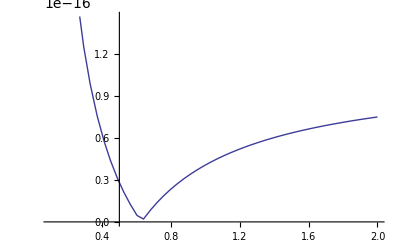

FindMinimum::precw: The precision of the argument function (0.0000103173372842340673613800965896727709167970221002577339869785675971367419382703303754802312624321445192718897311208376102613741599055881839022086473602135962536505421047752151964471031189873664872557380885663415865696354552239041574327926279343108199519169661295748163370566738370274686296068413728367505313846411125732077508837605957549381228745213181564917591590956296081754324308372453270331186268`200. « 1 ») is less than WorkingPrecision (400.).

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than 400. digits of working precision to meet these tolerances.

{3.380171545438213340266434473873062721096206507617920513166697333798902361145643664091528561873993666787262000668529686134015651947526124778808522985807281924185965419907017179482695242961468643202320325190274756015788998081216593066405534565020625199413855838831869332530606056765550558956775418224623550017110877746120306460656204161538205850412557786402090616062157251340144445034090350077500545474×10^-214,{d→6.281508200986272967069641613000906408512700065889136528765480967526495028515760308066869079470527229815221883059642038420289915216699766907704231775198476126326709874838469551499525952573161160549831964226559580951361951300749697733241818445480214857933134758039328513987472137482584477330004608337223549315254158571815438076463160453751224987019154193528250223420461545258447445145515885766715526305×10^-12}}

```mathematica
fun1=Abs[two[[1]]];
Plot[fun1,{d,10^(-12),2*10^(-11)}]
FindMinimum[fun1,{d,10^(-12)},WorkingPrecision->400]
```

```mathematica
eqnscompact
eqnsfull
```

{0.000010317337284234067361380096589672770916797022100257733986978567597136741938270330375480231262432144519271889731120837610261374159905588183902208647360213596253650542104775215196447103118987366487255738 ((By eta)/d-By ux),0.000010317337284234067361380096589672770916797022100257733986978567597136741938270330375480231262432144519271889731120837610261374159905588183902208647360213596253650542104775215196447103118987366487255738 ((By eta)/d+Bx uy),-(-1+gam) iec+(-1+gam) iein+By^2/(8 π)+(iein+(-1+gam) iein+By^2/(4 π)+rhoin) ux^2,-(-1+gam) iec+(-1+gam) ieout+Bx^2/(8 π)+(ieout+(-1+gam) ieout+Bx^2/(4 π)+rhoout) uy^2,(-dzsp L rhoin ux-d dzsp rhoout uy)/(dzsp L),rhoc-rhoout,(-dzsp L ux (iein+(-1+gam) iein+By^2/(4 π)+(rhoin ux^2)/2)-d dzsp uy (ieout+(-1+gam) ieout+Bx^2/(4 π)+(rhoout uy^2)/2))/(dzsp L),(-1+gam) iec-(-1+gam) iein-(-1+gam) ieout-By^2/(8 π)}

{0.000010317337284234067361380096589672770916797022100257733986978567597136741938270330375480231262432144519271889731120837610261374159905588183902208647360213596253650542104775215196447103118987366487255738 (-eta (-By/d+Bx/L)-(By ux)/(√(1+ux^2))),0.000010317337284234067361380096589672770916797022100257733986978567597136741938270330375480231262432144519271889731120837610261374159905588183902208647360213596253650542104775215196447103118987366487255738 (-eta (-By/d+Bx/L)+(Bx uy)/(√(1+uy^2))),-(-1+gam) iec+(-1+gam) iein+By^2/(8 π (1+ux^2))+ux^2 (iein+(-1+gam) iein+rhoin+By^2/(4 π (1+ux^2))),-(-1+gam) iec+(-1+gam) ieout+Bx^2/(8 π (1+uy^2))+uy^2 (ieout+(-1+gam) ieout+rhoout+Bx^2/(4 π (1+uy^2))),(-dzsp L rhoin ux-d dzsp rhoout uy)/(dzsp L),rhoc-rhoout,1/(dzsp L)(-dzsp L ux √(1+ux^2) (iein+(-1+gam) iein+By^2/(4 π (1+ux^2))+(rhoin (ux^2+ux^4))/(1+ux^2+√(1+ux^2)))-d dzsp uy √(1+uy^2) (ieout+(-1+gam) ieout+Bx^2/(4 π (1+uy^2))+(rhoout (uy^2+uy^4))/(1+uy^2+√(1+uy^2)))),(-1+gam) iec-(-1+gam) iein-(-1+gam) ieout-By^2/(8 π (1+ux^2))}

```mathematica
crapvars={{d,(1/2)*5.653357380887644979160738932189082495228737164855021459858289796288769612936894828593670336407251213975786160330384331195586808583367678941934415199724603329784514613105085101919602659495851050285694531062711497390396060809158434136740649701367387889052582388892950215091270626257759637920574246017751315721398573423`306.4051082624513*^-12},{ux,2.576412378997498322455771520403872627339147416814629578562054876304047447445501347820118999941062272407182341009059906924458884402782155277142973570654669046322685832586830200878386694363736079189106103387533023024173379737215040072802409740858460427254717282748211943039979891371263570687610765158447719669659319757`306.4051082624513*^-12},{rhoc,0.249999999653793364635516937100978296154267489264480026359947390920531776752882016648455371834986345231638453751074952085986167097457155595813948034651599169839318569891463114307351681373706265225849527204002599813897937629319435552785781341804001026065776172527916127784700188872074533327550287011390804321261001240307`306.4051082624513},{iec,2.492293127209970064458729781429824225787028267740788589905934534920392163967560290507846233872077509901900856531286420927399377083708150568468753469680816746998225022681902458268231707897986640622472334086727781962288318572484529616419746254387240586981570194228766840793042628545522614488700264495555581189181108547654`306.4051082624513},{rhoout,0.249999999653793364635516937100978296154267489264480026359947390920531776752882016648455371834986345231638453751074952085986167097457155595813948034651599169839318569891463114307351681373706265225849527204002599813897937629319435552785781341804001026065776172527916127784700188872074533327550287011390804321261001240307`306.4051082624513},{ieout,5.300089110573782648889010312304271209143595285854902572714054597151559932615396648836615105124728553456878169003314787225340450843349230519254597110138612291347375610994420710652021778274320570602006338942549712852676421529390710784388036403250270799235427065408204924449865368891320206692487345226753892148366048483792100942`306.4051082624513*^-23},{Bx,6.458108107361091401155401984759674233209890704785592175071758797332811681695582197871286615064424585122859781503309261391704866533422234992018630323690674315896603518021167958569847083789812011782059506294707703679862035802492936155005272250974415904257016983836931569568738421443991647115339260245851373747151353639`306.4051082624513*^-12},{uy,-1.82292553538220122982387380821933486209140622831747645443411613597269853377265301797109520266396056255072466899534967698639354969240474266641741580947524708822263290413137362059348184995140039689890903695159824093058600857975790093312263931906366412331012488074441555624582937442849944927721855668842429916240591315334`306.4051082624513}}
```

{{d,2.82667869044382248958036946609454124761436858242751072992914489814438480646844741429683516820362560698789308016519216559779340429168383947096720759986230166489225730655254255095980132974792552514284726553135574869519803040457921706837032485068369394452629119444647510754563531312887981896028712300887565786×10^-12},{ux,2.57641237899749832245577152040387262733914741681462957856205487630404744744550134782011899994106227240718234100905990692445888440278215527714297357065466904632268583258683020087838669436373607918910610338753302302417337973721504007280240974085846042725471728274821194303997989137126357068761076515844771967×10^-12},{rhoc,0.249999999653793364635516937100978296154267489264480026359947390920531776752882016648455371834986345231638453751074952085986167097457155595813948034651599169839318569891463114307351681373706265225849527204002599813897937629319435552785781341804001026065776172527916127784700188872074533327550287011390804321},{iec,2.49229312720997006445872978142982422578702826774078858990593453492039216396756029050784623387207750990190085653128642092739937708370815056846875346968081674699822502268190245826823170789798664062247233408672778196228831857248452961641974625438724058698157019422876684079304262854552261448870026449555558119},{rhoout,0.249999999653793364635516937100978296154267489264480026359947390920531776752882016648455371834986345231638453751074952085986167097457155595813948034651599169839318569891463114307351681373706265225849527204002599813897937629319435552785781341804001026065776172527916127784700188872074533327550287011390804321},{ieout,5.30008911057378264888901031230427120914359528585490257271405459715155993261539664883661510512472855345687816900331478722534045084334923051925459711013861229134737561099442071065202177827432057060200633894254971285267642152939071078438803640325027079923542706540820492444986536889132020669248734522675389215×10^-23},{Bx,6.45810810736109140115540198475967423320989070478559217507175879733281168169558219787128661506442458512285978150330926139170486653342223499201863032369067431589660351802116795856984708378981201178205950629470770367986203580249293615500527225097441590425701698383693156956873842144399164711533926024585137375×10^-12},{uy,-1.82292553538220122982387380821933486209140622831747645443411613597269853377265301797109520266396056255072466899534967698639354969240474266641741580947524708822263290413137362059348184995140039689890903695159824093058600857975790093312263931906366412331012488074441555624582937442849944927721855668842429916}}

```mathematica
(* check -uy for relativistic outflow *)
vel4togorel=2.0;
If[(Abs[mysolnonrel[[8,2]]]>vel4togorel||Abs[mysolnonrelconverted[[8,2]]]>vel4togorel),mysol=mysolmixedrel;Print["Using mixedrel"];,mysol=mysolnonrelconverted;Print["Using convertedrel"];];
(* form guess for rel calculation *)
myvars=formnonrelguess[mysol];
(* start rel calculation process *)
solvespfullsetup1;
solvespfullsetup2;
```

Using mixedrel

Slund=1.×10^25

sigma=225702.

```mathematica
(* check -uy for relativistic outflow *)
mysol=mysolnonrel;
myvars=formnonrelguess[mysol];
(* start rel calculation process *)
solvespfullsetup1;
solvespfullsetup2;
```

Slund=1.×10^25

sigma=13848.9

```mathematica
vel4togorel=0.5;
If[( Abs[mysolnonrel[[8,2]]]>vel4togorel||Abs[mysolnonrelconverted[[8,2]]]>vel4togorel),
(* then average converted and mixedrel solutions *)
mysol=Table[mysolnonrelconverted[[ii,1]]->(mysolnonrelconverted[[ii,2]]+mysolmixedrel[[ii,2]])*0.5,{ii,1,8}];
(* now try again *)
(* form guess for rel calculation *)
myvars=formnonrelguess[mysol];
(* start rel calculation process *)
solvespfullsetup1;
solvespfullsetup2;
];
```

Slund=1.×10^25

sigma=13848.9

```mathematica
(*
FindRoot[nummyeqns0,myvars,MaxIterations->2000,DampingFactor->0.8,WorkingPrecision->workprec,AccuracyGoal->whichaccuracy,PrecisionGoal->whichprecision]
*)
```

```mathematica
myvars
```

{{d,4.13206×10^-14},{ux,7.10134×10^-12},{rhoc,15.2166},{iec,41546.6},{rhoout,15.2339},{ieout,2.14638×10^-18},{Bx,4.06552×10^-9},{uy,-240.262}}

```mathematica
SetPrecision[mysolnonrel,10]
SetPrecision[mysolnonrelconverted,10]
Print["mixed"];
SetPrecision[mysolmixedrel,10]
SetPrecision[mysol,10]
Print["actual result"];
SetPrecision[res,10]
SetPrecision[myvars,10]
```

{d→4.122470368×10^-14,ux→2.425686201×10^-12,rhoc→0.25,iec→41546.59114,rhoout→0.25,ieout→4.889340764×10^-19,Bx→6.080293617×10^-12,uy→-235.3623905}

{d→6.786038622×10^-14,ux→7.437240514×10^-12,rhoc→15.30510595,iec→41546.59114,rhoout→15.33977017,ieout→4.893604838×10^-19,Bx→4.139661735×10^-9,uy→-450.266821}

mixed

{d→1.47807464×10^-14,ux→6.765436072×10^-12,rhoc→15.1281115,iec→41546.59114,rhoout→15.1281115,ieout→3.803405766×10^-18,Bx→3.991377412×10^-9,uy→-30.256223}

{d→4.132056631×10^-14,ux→7.101338293×10^-12,rhoc→15.21660873,iec→41546.59114,rhoout→15.23394084,ieout→2.146383125×10^-18,Bx→4.065519573×10^-9,uy→-240.261522}

actual result

{d→1.485887028×10^-14,ux→6.729865257×10^-12,rhoc→14.81245398,iec→41546.59114,rhoout→14.81245398,ieout→3.763516369×10^-18,Bx→3.972514596×10^-9,uy→-30.5769078}

{{d,4.132056631×10^-14},{ux,7.101338293×10^-12},{rhoc,15.21660873},{iec,41546.59114},{rhoout,15.23394084},{ieout,2.146383125×10^-18},{Bx,4.065519573×10^-9},{uy,-240.261522}}

```mathematica
FindRoot[crapeq,crapvars,WorkingPrecision->myprec,MaxIterations->2000,AccuracyGoal->whichaccuracy,PrecisionGoal->whichprecision];
```

```mathematica
FindRoot[nummyeqns0,myvars,MaxIterations->maxiter,WorkingPrecision->workprec,AccuracyGoal->whichaccuracy,PrecisionGoal->whichprecision]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 3000 iterations.

{d→1.707218208798944097722281829187×10^-16,ux→4.90702613301428749887641665874×10^-12,rhoc→0.2399135231002482811016462231295,iec→41546.59114181615404957068758826,rhoout→0.2399135231002482811016462231297,ieout→3.648859137999564513110278127889×10^-18,Bx→2.895003767127977564635829058083×10^-9,uy→-240.2590229048243186553545957251}

```mathematica
rootmyprec=SetPrecision[nummyeqns0,workprec];
varmyprec=SetPrecision[myvars,workprec];
FindRoot[rootmyprec,varmyprec,MaxIterations->maxiter,WorkingPrecision->workprec,AccuracyGoal->whichaccuracy,PrecisionGoal->whichprecision]
```

{d→1.485887027930279634256911570493789789100537904455706542979266100270338624338123823496133446080350777963147112279564518462794834090162564561094557831709810144605649090439116486508080858022757069894920671524818899743500200503165451346368415508465656538475599661256260594669079838731365292520430270102911652121749207025476548307709067890397227106598215347269642584633571961760704058134750763599975905045922034267375853798631337926401569511682053947309546187512709786222721281719916209007274577311042723×10^-14,ux→6.7298652567089602062243226112107992835214577014027784610621573679762297783211445798997029902996765308969563508690751321026711742938810251421240808273416651710642320559313671042231997251652289709620627396141354400666296410829222334867378213857874144327454272853716837097065035625627913705117685271347860389153014456679008527762187497937364166923333687139233611675338063755213237882480413374498406694448469598780288603091919523650622748564316692674081296526066525423741455834606129564769558355964656187×10^-12,rhoc→14.812453980751160398724480530241568338406540926663864190777964160330104033032596268863618345718160508771153736101037962603049019780508756642913415606365131389570702935886260075096936161147713962022201728970474492841481431795985997644188610042074603927839901210425154037845831183322326781375804386451559938387445698842039821526410301877762808480023218286527441663901022069912434532545765016101246019944716751625839917620291826399058574356524968137596161768761037829078018424130117278430043414915724041,iec→41546.591141816151865053853652398153386257008132226376417643666783373739955438197059429903216543554665163094434168031223345297262925936005363201301761828907960689981652124996141040618806104323237100942011794801749901215724195767889968886838739339653184683690009814030296293102898236774436809503518205687616843520712310090913582140590758364531152854087015829898646531620617548707892284694512820531292415900895963181929653532664535294400384602513461138490772819184266295679904587364819808375944638604535,rhoout→14.812453980751160398724480530241568338406540926663864190777964160330104033032596268863618345718160508771153736101037962603049019780508756642913415606365131389570702935886260075096936161147713962022201728970474492841481431795985997644188610042074603927839901210425154037845831183322326781375804386451559938387445698842039821526410301877762808480023218286527441663901022069912434532545765016101246019944716751625839917620291826399058574356524968137596161768761037829078018424130117278430043414915724041,ieout→3.7635163691126309234635898679109162944829606652286910510547929835254462761900023065666976932307709916990919085477715382886558411221490706964363880219950247639628190196234248342807519673380361599760989536331507701196248538095071912321006792110696884112332498551550141043718831555029378245503381332042965836622659609421464378580295689322363970781403936009488611604579260088959381889208136035051117457737457362444339449721845757195781576661979011440769934181396956134445189548248619861339222533320108511×10^-18,Bx→3.9725145957721367760662235024166759832379315679293605562682469755160128369276102327593328634068823358401297463786735762593906395883580469468358449748618526792140469439385550507162489776188777155631032111300349654356896123154619557077581731934686538497814517958704885972033761033899366442773053396373932737592735620943684671142835539246848559400449911914921847504809582243945121027513952570704307622762190650137168519184093490068678213226196401091321377668902791500674258174305119328299593498685436249×10^-9,uy→-30.576907797079546565191525826368387589226581166606333298919720924657021059222362980382241365816223273589003470503066074103426192097413725169254791768347982647076167083524219578959019580444378129054210163138279146310397476669235605825663266487231749402589951439818395099067860093986407021881836910546399305830726184273340518288405965842627760189567440749174159179460352263857080229089669592248029943311226513597462269026152985679030214624862570464783399697046510883270969684548774452753966280199124896}

```mathematica
(*crapeq=SetPrecision[nummyeqns0,5000];
{res,{evx}}=Reap[FindRoot[crapeq,crapvars,WorkingPrecision->500,DampingFactor->0.8,MaxIterations->3,EvaluationMonitor:>Sow[{d,ux,rhoc,iec,rhoout,ieout,Bx,uy}]]];*)
myprec=500;
crapeq=SetPrecision[nummyeqns0,myprec];
crapeqnot0=Table[crapeq[[ii,1]],{ii,1,8}];
crapvars=SetPrecision[myvars,myprec];
(*crapvars=SetPrecision[shitvars,myprec];*)
{res,{evx}}=Reap[FindRoot[crapeq,crapvars,WorkingPrecision->myprec,MaxIterations->5000,AccuracyGoal->whichaccuracy,PrecisionGoal->whichprecision,StepMonitor:>Sow[{Log[10,crapeqnot0.crapeqnot0],d,ux,rhoc,iec,rhoout,ieout,Bx,uy}]]];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 5000 iterations.

```mathematica
(*
mysolmixedrel: started: d: below, ux: above,  rhoc: above, rhoout: above, ieout: above, Bx: above, uy: above

averagedrel: started: d: above, ux: below, rhoc: below, rhoout: below, ieout: below, Bx: below, uy: below
*)
```

{5000,9}

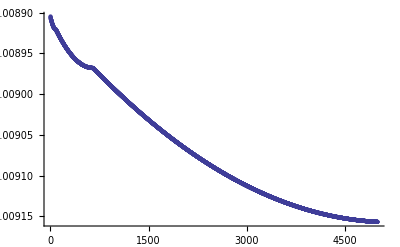

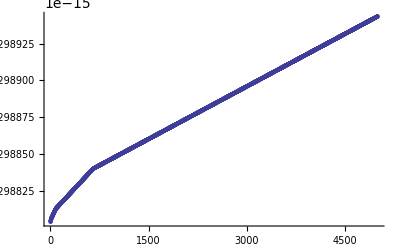

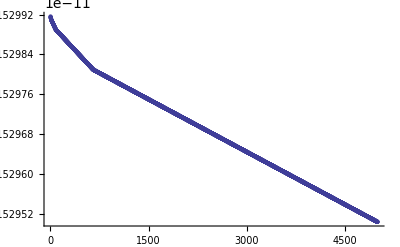

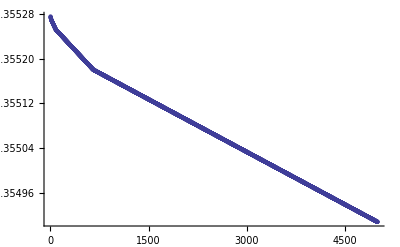

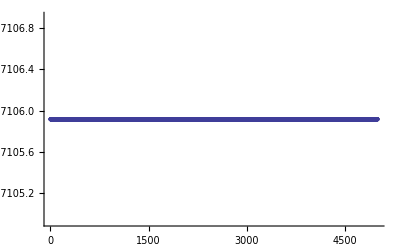

-Graphics-

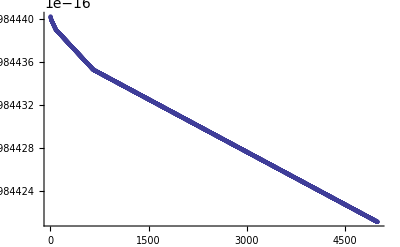

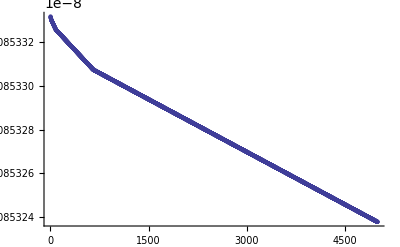

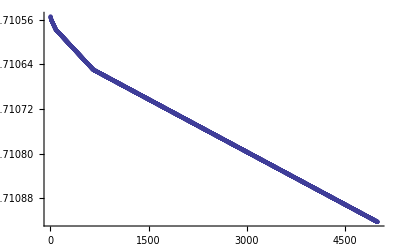

```mathematica
dim=Dimensions[evx]
which=1;mytable=Table[evx[[i,which]],{i,1,dim[[1]]}];ListPlot[mytable,PlotRange->All]
which=2;mytable=Table[evx[[i,which]],{i,1,dim[[1]]}];ListPlot[mytable]
which=3;mytable=Table[evx[[i,which]],{i,1,dim[[1]]}];ListPlot[mytable]
which=4;mytable=Table[evx[[i,which]],{i,1,dim[[1]]}];ListPlot[mytable]
which=5;mytable=Table[evx[[i,which]],{i,1,dim[[1]]}];ListPlot[mytable]
which=6;mytable=Table[evx[[i,which]],{i,1,dim[[1]]}];ListPlot[mytable]
which=7;mytable=Table[evx[[i,which]],{i,1,dim[[1]]}];ListPlot[mytable]
which=8;mytable=Table[evx[[i,which]],{i,1,dim[[1]]}];ListPlot[mytable]
which=9;mytable=Table[evx[[i,which]],{i,1,dim[[1]]}];ListPlot[mytable]
```

```mathematica
SetPrecision[mysolnonrel,10]
SetPrecision[mysolmixedrel,10]
```

{d→4.122470368×10^-14,ux→2.425686201×10^-12,rhoc→0.25,iec→41546.59114,rhoout→0.25,ieout→4.889340764×10^-19,Bx→6.080293617×10^-12,uy→-235.3623905}

{d→1.47807464×10^-14,ux→6.765436072×10^-12,rhoc→15.1281115,iec→41546.59114,rhoout→15.1281115,ieout→3.803405766×10^-18,Bx→3.991377412×10^-9,uy→-30.256223}

```mathematica
mysol
res
```

{d→0.0000193908490992158377573090562791262420510800311170427402104421134265426827210576673405325392517088084766233197663121250117284289885847814469720400415865197312363869776593280599817049416219378851155163851589581124055587853481834695694589181819894921110966318236133822187958752233747575125006604227274758531341352250266077183353182001390769892175499771316087721074683583433790633,ux→0.000751147093378434018169273918272302582246482031334252966026094382676208782733679985540624904824509765265322703052172790339303256730150496209241283209452987620139534552626305923274914765684255266794417133745575938473235242908589547915356896834155286117650291285266275473472477566518094495619226917402179503415352193736116787285239965324455237917659082547566135483278545762075663,rhoc→0.212501276318767366791274531493481045601301141462220825830072819446473607219441771388968041881339357247965067757641872276649771238429749800099469857499299552659900094465629333974921681333518631155970137429525551121669241088982500718023968725015227073715967554821378230762767207947189699481799648480202102286518777624859029084957305302607406328307148154268134190612755364400956,iec→24922.9593634118949736628168184664745053259359499164605365836701895174149379756085452745352212387646019874822125349375367545645014543642479174338126904281435830700455399848231632189982173738054294548488226105822108103955979003034899411926617074338424103846260986432305566260725538517360308143104021084140797449851792249280242167573001156796362688668288475619870567528020700804,rhoout→0.212501276318767366791274531493481045601301141462220825830072819446473607219441771388968041881339357247965067757641872276649771238429749800099469857499299552659900094465629333974921681333518631155970137429525551121669241088982500718023968725015227073715967554821378230762767207947189699481799648480202102286518777624859029084957305302607406328307148154268134190612755364400956,ieout→0.0281258226846840519901199021859221773851644507737025734457491865098597641939488120716378357905351338498939501926590273929085398909421717827471578502858553867288938457043677445673736501092375953757511107438427428270352040952230381651071131354338051407688764264027864846589889619829182759798606575703145614959702363916972739315882344944017260883771311258022043950827531863912716,Bx→0.00188285654187534583824446857280388694309079326453745564768535156354027952601320878131670598087897062538279139606840098370416920588342309739706153933276859059640880319354545404303688256156558167709092548094022252718653487175136100395061423332197862108536915611581392861747655772577046937261930035322759132325308546271920055908474726888181911419201970914463848490003391822770097,uy→-182.291585192475254157597969842306338368264215146174806331275670075738337774721728189348329272965886124165093189035528196512355184066323576494540227277858845137480743619369761985762835649461863104391360402960130142922970279768842025073505451249953041956756997124846232517317821483078955190488045785769401707714953041262763098132906006049783888210382414764647146774531778962356}

{d→6.813934253317068450067674658524207613113693857132131497963788067358029342795664489705059920390918850161038589875682902481659133350563145689547421798982421022833678911530120058726090784893402035605338837453187876784723226573977327338200544432898572278340073308635681964415317808845537326317588559947047081702493585161946807676265827200147447030900478366648665245515330667453561346868737108427205800962×10^-6,ux→0.002137592242892164172352239228973369399062770529158466698799075116293206498826354041061871361370548801946148424179206941712616072961805055844950340847534149446597520931645890721163227170175542446178177223682114723289892213245059657780426817237961336784495261766041266701383680740675619814466851688836743044887650733927866895240857196353353949779430892402917047858455060704386128284885421779375853254158,rhoc→12.14261889566766656390730778123637706054509037070519843667659088350845596454511009150446260645454195410276660802921170505046614270544625487949604965979058927790597551787352269558844497210195805375814226383134240929041963930512843710542447628019686480611677712089495685511301618101993437200031483704109426035983436444256760526070727196309120028790610879193710412950401224926735499582987706595392928865,iec→24922.93125077676328073630302698134096077827102861159524800800631510306664063510880215099660184429688708104684659836359393526795626872107878839306287186855778968738163814103142282473020466660928151739935762048231491629047420295631034849684395632687531756365541938808661003124040681901332325254889594348461606765330816913228196713281349358101581721685172095897308376214528972243711077133927886713496392,rhoout→12.14261889566766656390730778123637706054509037070519843667659088350845596454511009150446260645454195410276660802921170505046614270544625487949604965979058927790597551787352269558844497210195805375814226383134240929041963930512843710542447628019686480611677712089495685511301618101993437200031483704109426035983436444256760526070727196309120028790610879193710412950401224926735499582987706595392928865,ieout→0.2277723556610865179952815510138470658999070928734502321056388329610092080712471457025601032567905491353993360581169470406927341397134461239424363735452519504888128197926946062842497824317876085839100550408065908115047802655108193257384686044533576389217418508526613987019559373227735489676730675383180367246826726532177859293961085423011363141627887928856665316257453061162266024015554296685566667612,Bx→0.9774776360040203716719778233879641701738015776584611590431600304655105990575942496087670148903191242964188948955141436687253148187259738416954787134768503236651041630808322765054945915708322981960373328395535683227004465662096542808518922767916107336268160093594514521403584378695718800655919097084610231643396741291803129093373657327755408793261671568774996317008835915082899798656180049211754673834,uy→-25.83536260702207132348217845103474488922810817390095152046363870645851121563251987121916873599084939427830376681040903166880877786233299356849728900985769378335967096713710232543092315606276218835954765826180256203042477946769312112318394825630700934444692205490217273858240033582864843187603655232856852699632674055816410084240384236164676829471602526751260471213613036576308800179249127459217592052}

```mathematica
rat=Table[res[[ii,2]]/mysol[[ii,2]],{ii,1,8}]
```

{0.351399478096739077449292343226739557452764865927965347163499819613092691050846243468226125712183579242248750989737709939377546772049196522767568235180211687394203821419686328146513872035806801516612158363031101852377942286384653449283650945031189977205494430855934748324306064078764976252966726276962445862474437466327553947178073749256790076876735153201474186991456089093795,2.84577050451984882478829077176810207897457495161052713180856786243608227863359244402137001951849111868439263711255133942920602401896600435075211930729589406367985207592437668865549661872995317576522067772631421516245507777813979088371662714595370029332370541745732438638233674037390317861526123245505013762300136043638827697012825729135861527090177375452469880067484162442874,57.1413927766384577084248260466907578395242817286837654619981584921823202337995397566488974297957413588150813831609958947349744282241117593861386948940960295302226629049734480798158591568838384523401090163511480627453188168826479694704549546378893053112865121553190101865685994444198726966803269722614676999452321999663730187475682118187771544972626941446434225057315612502503,0.999998872018578461287015826578336127422038610950432288162586630340148498266119493374945652474101764889467959143935421510848001077059244215764635572185621932740747669106790835256874142255959604842102470180167125669877452172867960004713054772425047988493286990408924131742298312232703090613075573809226053379856205464865489033358539264974059583245599107445049838621273563392482,57.1413927766384577084248260466907578395242817286837654619981584921823202337995397566488974297957413588150813831609958947349744282241117593861386948940960295302226629049734480798158591568838384523401090163511480627453188168826479694704549546378893053112865121553190101865685994444198726966803269722614676999452321999663730187475682118187771544972626941446434225057315612502503,8.0983357612191805319411078452030239788394054339876553513239921701742161861009895759832798100610411004004658956062631991736875172363637744382550565268452935842017894918301027534339585387204565926297238638683449929059452292763122221554003151017486488955906777763777446477894548499025233648865686302933040960635082758799542036361171589301886471553072612295093918108116812994057,519.146102883888269144415672657799195302958717794530001766902024289268587212817956467938590603583440432489548654297103059788217837116009039325812070409963499778283556008977422915039866990433358842703564249628842077968648373028889084368867043919175952815553134488861612015952933238059218795181595325209635334642291542431659369879427810327997000896515695653420496716776767042029,0.141725481073322300276705740362791467347623130062902996157279388188303544260309959796363052690826274143106404505314443980007512298075455076047657057731955639357533250061575366241850526791701980500391210241353915280279052092043076879827501799576950572450623117026943522479882586567732986483094814588991625128929379692146872628899280323793683489108907952245685730612677970925146}

```mathematica
Sqrt[2]*sigma^(3/2)
```

3.02884×10^6

```mathematica
sigma^(2/5)
```

48.7757

```mathematica
sigma^(2/3)
```

651.136

```mathematica
rat=Table[res[[ii,2]]/mysol[[ii,2]],{ii,1,8}]
```

{0.839225710151070841272168218515876179520652399543737494125423995874661042021780262866534257564649043281680076931283615746283458243787219711513352896303265591336631509973773319699418972410420710079555944896195302911247269390045403750950276937965162791169625919647572209930113419708340743506154615425601311564889293710242458208575148185357113932995293260603780964900168,1.19157453609252475644738691952016639355404475798187962962885165164989323332159750649400573453147292429479535798982034324541063500578833604749089163106849413074028313972004673960398160427436329847573430970161555816357403300852892037541554622440527173265025407585547198678875650946738607942915249309674360428894597106951184621381249531209025320691131477688197178231583,2.01597361138786728768187635271961912938742820624321115131491459806368782184783066257359376022859444974157783334687464354908247377610155873300784157477107600377614332474216455766579851754218721567984486041889244865463174805722042145411406826864367960783994699974529899327242420608443070670446347437308482450108077605438621024840707993725288800102423990979729094006854,0.999999990078848441196403061835477550176052789698354418438093946858693044990502266033103916299230273280612317453107196943348784189345183720147378840259152148412293535714079744028523812023944215302397872130991151267177118040004690274050822768227530857428853480769554722591912493246119418500255687971895645472936077828220314884403289904360631908302736231706022173539734,2.01597361138786728768187635271961912938742820624321115131491459806368782184783066257359376022859444974157783334687464354908247377610155873300784157477107600377614332474216455766579851754218721567984486041889244865463174805722042145411406826864367960783994699974529899327242420608443070670446347437308482450108077605438621024840707993725288800102423990979729094006854,1.41984985835620256668115334000497856278895707889415167906472649215475232093211964016441470618275715076434590225744926107386429722570109450704698016849213367824929701535608303445965259547481376305761264069255622568950415815577280621125450108589641304670424557371483626989243143150162023836521527681478766325058066948564495848168193977024814339906902556184268839681441,2.75329285304339985367395869782132502336976822072332645053709280849241357676831252986912826354461739803550019812903964305544962511907329399426881878402110306818139627815988004760301297693455756072646699618588381225642098015887237427365138312133811375125683163972955560778372580581655799587125504691397509894336981301953133496028432141044616077780463899552678378353235,0.704299841310580786019630254298644129963937315061176915131796049432358629396432061224343904985783812670147987192908844181072267900117058386207627331084190423752154880411561377757013476099495989594803349588017805479737464602946661621469158640244691510909787487706035410088723792826017771358926770483685297317167007974453406074712258889041638338155722612143848043140435}

```mathematica
(* CHECK CONVERGENCE *)
```

```mathematica
sigma^(3/2)
```

2.14172

```mathematica
(* http://www.scipy.org/ *)
```

```mathematica
(*fsols=FindRoot[eqns,{{d,0.0001,1},{vx,-.999,0},{rhoc,.01,100},{iec,0.001,100},{rhoout,0.01,100},{ieout,0.01,100},{Bx,0.01,100},{vy,0,0.999}},MaxIterations->10000,DampingFactor->1.5,WorkingPrecision->20,Method->"Secant"]*)
```

```mathematica
(*fsols=FindRoot[eqns,{{d,0.001*olddelta,1},{vx,-vextreme,vextreme},{rhoc,.1*rhoold,10*rhoold},{iec,0.1*ieold,10*ieold},{rhoout,0.1*rhoold,10*rhoold},{ieout,0.1*ieold,10*ieold},{Bx,0.01*Bxold,10*Bxold},{vy,-vextreme,vextreme}},MaxIterations->10000,DampingFactor->1.5,WorkingPrecision->20,Method->"Brent"]*)
```

```mathematica
vaold2=c*By/Sqrt[1.0*4*Pi*rhoout*c^2]//.consts//.fsols
olddelta=Sqrt[eta*L/vaold2]//.consts//.fsols
olddelta=1.0*Sqrt[eta*L/vaold]//.consts//.fsols
```

```mathematica
gamx//.consts//.fsols
gamy//.consts//.fsols
(rhoc/rhoin)//.consts//.fsols
(rhoout/rhoc)//.consts//.fsols
```

```mathematica
(* Check that numerical satisfies original equations *)
result=eqns//.consts//.fsols
```

```mathematica
(* DONE! *)
```

```mathematica
(* DONE! with numerical result *)
```

```mathematica
(* ANALYTICAL: try to get analytic solution: Works only if remove extra non-Dmitri terms *)
```

```mathematica
eqns={eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8};
sols=Solve[eqns,{d,vx,rhoc,iec,rhoout,ieout,Bx,vy}];
eqnsother={eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8}//.{iein->0};
solsother=Solve[eqnsother,{d,vx,rhoc,iec,rhoout,ieout,Bx,vy}];
```

```mathematica
sols//.consts
solsother//.consts
```

```mathematica
(*
eqnsraw={eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8};
array=CoefficientArrays[eqnsraw,{d,vx,rhoc,iec,rhoout,ieout,Bx,vy}]
mymatrix=Normal[array][[2]]
myb==Normal[array][[1]]
Det[mymatrix]
*)
```

```mathematica
(*
array=CoefficientArrays[eqns,{d,vx,rhoc,iec,rhoout,ieout,Bx,vy}]
mymatrix=Normal[array][[2]]
myb==Normal[array][[1]]
Det[mymatrix]
*)
```

```mathematica
(*mymatrix.{d,vx,rhoc,iec,rhoout,ieout,Bx,vy}*)
```

```mathematica
(*NSolve[mymatrix.{d,vx,rhoc,iec,rhoout,ieout,Bx,vy}==myb,{d,vx,rhoc,iec,rhoout,ieout,Bx,vy}]*)
```

```mathematica
(*array=CoefficientArrays[{eq1,eq2,eq3,eq4,eq5,eq6,eq7},{vx,rhoc,iec,rhout,ieout,Bx,vy}]
Normal[array]*)
```

```mathematica
(*
eq1=x*1==2
eq2=y*3==5
eqns={eq1,eq2}
array=CoefficientArrays[eqns,{y,x}]
MatrixForm[Normal[array]]
N[Det[Normal[array]]]
*)
```

```mathematica
(*
mymatrix=Normal[array][[2]]
MatrixForm[mymatrix]
Det[mymatrix]
*)
```